# Large volume scattering diagrams for local F0

```mathematica
SetDirectory[NotebookDirectory[]];
<<F0Scattering`
<<MaTeX`
```

F0Scattering 1.17, Nov 28, 2024 - A package for evaluating DT invariants on F0,F1

### Figure 1

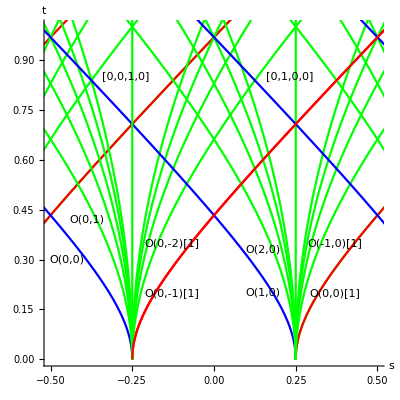

```mathematica
(* in (s=x+m/2,t) plane *)
GrF0s[m_]:=With[{Nm=5,tm=1.1},
{Table[{Table[
ParametricPlot[
{Rays[-{1,-k+p,-1+p,(p-k)(p-1)},t,0,m]+m/2,t},{t,0,tm},
PlotStyle->If[k==1,Red,Green]],{k,1,Nm}],
Table[ParametricPlot[{Rays[-{1,p,p-k,p(p-k)},t,0,m]+m/2,t},{t,0,tm},PlotStyle->If[k==1,Red,Green]],{k,0,Nm}],
Table[ParametricPlot[{Rays[{1,p,k+p,p(k+p)},t,0,m]+m/2,t},{t,0,tm},PlotStyle->If[k==0,Blue,Green]],{k,0,Nm}],
Table[ParametricPlot[{Rays[{1,k+p,p,p(k+p)},t,0,m]+m/2,t},{t,0,tm},PlotStyle->If[k==1,Blue,Green]],{k,1,Nm}],
ParametricPlot[{Rays[{0,0,1,p},t,0,m]+m/2,t},{t,0,tm},PlotStyle->Green],ParametricPlot[{Rays[{0,1,0,p},t,0,m]+m/2,t},{t,0,tm},PlotStyle->Green]},{p,-2,2}],
ParametricPlot[{Rays[-{1,0,-1,0},t,0,m]+m/2,t},{t,0,tm},PlotStyle->Red]}];
Show[GrF0s[1/2],Graphics[{
Rotate[Text["O(0,0)[1]",{-.88+1+1/4,.2}],50 Degree],
Rotate[Text["O(-1,0)[1]",{-.88+1+1/4,.35}],60 Degree],Rotate[Text["O(0,0)",{-.7+1/4,.30}],-45 Degree],
Rotate[Text["O(0,1)",{-.64+1/4,.42}],-60 Degree],
Rotate[Text["O(1,0)",{-.1+1/4,.2}],-50 Degree],
Rotate[Text["O(2,0)",{-.1+1/4,.33}],-60 Degree],Rotate[Text["O(0,-1)[1]",{-.38+1/4,.2}],55 Degree],Rotate[Text["O(0,-2)[1]",{-.38+1/4,.35}],60Degree],
Rotate[Text["[0,0,1,0]",{-.52+1/4,.85}],90Degree],Rotate[Text["[0,1,0,0]",{-.02+1/4,.85}],90Degree]}],
PlotRange->{{-1/2,1/2},{0,1}},AxesLabel->{"s","t"}]
```

### Figure 13

```mathematica
(* use list of exceptional bundles and periodicize it *)
ListExcep0=Take[{{1,0,0,0},{3,1,1,4/9},{3,2,2,4/9},{5,1,2,12/25},{5,2,1,12/25},{5,3,4,12/25},{5,4,3,12/25},{7,1,3,24/49},{7,3,1,24/49},{7,4,6,24/49},{7,6,4,24/49},{9,1,4,40/81},{9,4,1,40/81},{9,5,8,40/81},{9,7,7,40/81},{9,8,5,40/81},{11,1,5,60/121},{11,5,1,60/121},{11,6,10,60/121},{11,10,6,60/121},{11,4,4,60/121},{11,7,7,60/121}},7];
With[{n=3},ListExcep=Flatten[Table[Table[ListExcep0[[k]]+ListExcep0[[k,1]]{0,i,j,0},{i,-n,n},{j,-n,n}],{k,Length[ListExcep0]}],2]];
ListDiscBound[eta_,a_,b_]:=Simplify[excDiscBoundB[0,#,eta,{a,b}]&/@ListExcep];
excDiscBoundB[e_,{r_,d1_,d2_,dis_},m_,{a_,b_}]:=If[(m a+b)+m+e/2+1>=(m d1+d2)/r≥(m a+b),
(a-d1/r+1)(b-d2/r+1-(a-d1/r) e/2)-dis,If[(m a+b)>=(m d1+d2)/r≥(m a+b)-(m+e/2+1),(d1/r-a+1)(d2/r-b+1-(d1/r-a) e/2)-dis,0]];
```

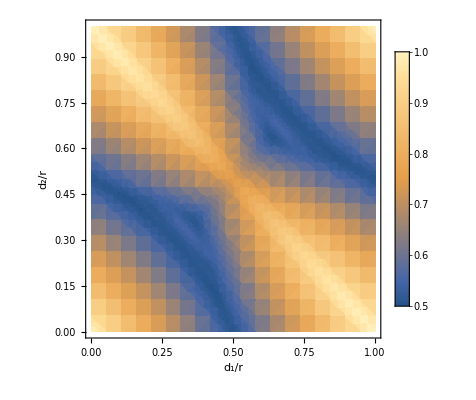

```mathematica
DensityPlot[Max[ListDiscBound[1,a,b],1/2],{a,0,1},{b,0,1},PlotLegends->Automatic,PlotPoints->20,AxesLabel->{"d_1/r","d_2/r"}]
```

### Figure 14

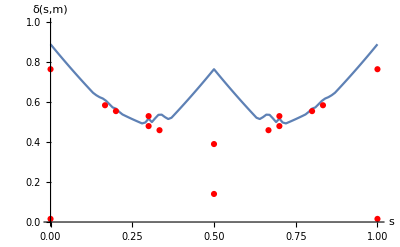

```mathematica
With[{m=1/4,step=.01},
(* compute \delta(s,\eta,M1)for s=mu ranging from 0 to 1 in steps of 0.01 *)
Delmin=Table[{mu,Min[Table[Max[ListDiscBound[1,a,2mu-a]]+(mu-a+m/2)^2,{a,-1,2,step}]]},{mu,0,1,step}];
Gr=ListPlot[Delmin,Joined->True,PlotRange->{0,1},AxesLabel->{"s","δ(s,m)"}]; 
Ta=Table[{(ListExcep[[k,2]]+ListExcep[[k,3]])/2/ListExcep[[k,1]],ListExcep[[k,4]]+1/4(ListExcep[[k,3]]/ListExcep[[k,1]]-ListExcep[[k,2]]/ListExcep[[k,1]]+m )^2},{k,Length[ListExcep]}];
(* keep only the minimum for each slope *)
Ta1=Union[Table[First[Ta[[k]]],{k,Length[Ta]}]];
Ta2=Table[{Ta1[[l]],Min[Transpose[Select[Ta,First[#]==Ta1[[l]]&]][[2]]]},{l,Length[Ta1]}];
(* keep all those that lie below the DLP curve *)
Ta3=Select[Ta,#[[2]]<=.02+Delmin[[Floor[1/step Mod[#[[1]],1]]+1,2]]&];
Show[Gr,ListPlot[Ta3,PlotStyle->Red,PlotRange->{{0,1},{0,1}}]]]
```

### Figure 18

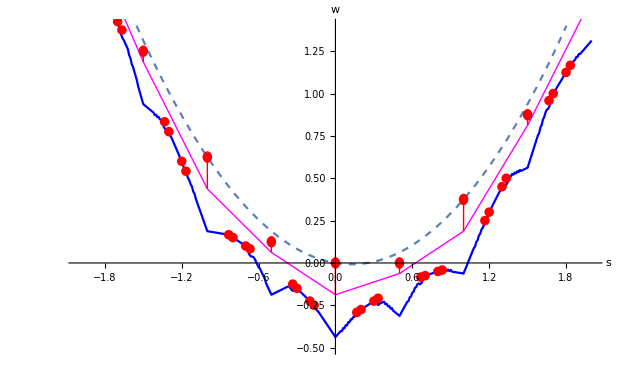

```mathematica
With[{m=1/4,step=.01},Show[Plot[1/2(s-m/2)^2-m^2/8,{s,-2,2},PlotStyle->Dashed,PlotRange->{-1/2,1.4},AxesLabel->{s,w}],ListPlot[Table[{s,1/2(s-m/2)^2-1/2Delmin[[Floor[Mod[s,1]/step]+1,2]]},{s,-2,2,.01}],Joined->True,PlotStyle->Blue],
ListPlot[Map[{#[[1]],1/2(#[[1]]-m/2)^2-1/2#[[2]]}&, Ta2],PlotStyle->Red],
Graphics[Flatten[{Table[{With[{t=k+1/2-m,td=1/2(k^2+k+1/2)-m/2(k+1/2)},{Magenta,Line[{{k,-td+k t},{k+1/2,-td+(k+1/2)t}}]}],With[{t=k+1/2,td=1/2(k^2+k+1/2)+m/2(k+1/2)},{Magenta,Line[{{k+1/2,-td+(k+1/2) t},{k+1,-td+(k+1)t}}]}],Red,
Circle[{k,1/2k(k-m)},.03],Circle[{k+1/2,1/2k(k+1-m)},.03],
Line[{{k,1/2k(k-m)},{k,1/4 (-1+2 k^2+m-2 k m)}}],Line[{{k+1/2,1/2k(k+1-m)},{k+1/2,1/4 (2 k^2-2 k (-1+m)-m)}}]},{k,-2,1}]}]]]]
```

### Figure 24

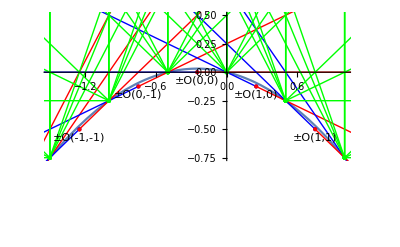

```mathematica
With[{L=3,m=1/2},Show[Plot[-1/2x(x+m),{x,-2,2}],Graphics[
Flatten[{Table[{Blue,
Rayxy[{1,k,k,k^2},k-m/2,L,m],
Rayxy[{1,k+1,k,k(k+1)},k+(1-m)/2,L,m],Red,
Rayxy[-{1,k,k,k^2},k-m/2,L,m],
Rayxy[-{1,k+1,k,k(k+1)},k+(1-m)/2,L,m]},{k,-2,1}],
Table[{Green,Table[{Rayxy[{1,k+p,p,p(k+p)},p,L,m],
Rayxy[-{1,-k+p,p,p(-k+p)},p,L,m],
Rayxy[{1,p,p+k,p(k+p)},p-m,L,m],
Rayxy[-{1,p,-k+p,p(p-k)},p-m,L,m],
Rayxy[{0,1,0,p},-1/2 p(p+m),L,m],
Rayxy[{0,0,1,p},-1/2 (p-m)(p),L,m]
},{k,2,4}],Black,
Text["±O("<>ToString[p]<>","<>ToString[p]<>ToString[")"],{-m/2+p,-p^2/2-.07}],Text["±O("<>ToString[p+1]<>","<>ToString[p]<>ToString[")"],{(1-m)/2+p,-p(p+1)^2/2+(m-1)/4-.07}]},{p,-1,1}]}]
],
PlotRange->{{-1-m,1},{-1.5m,m}}]]
```

### Figure 25

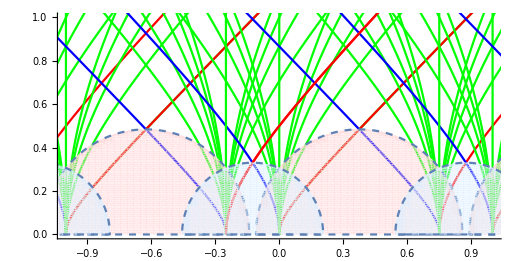

```mathematica
CollI={{1,0,0,0},{-1,1,0,0},{-1,0,1,0},{1,-1,-1,1}};
CollII={{1,0,0,0},{-1,1,0,0},{-1,-1,1,1},{1,0,-1,0}};
GrF0[m_]:=With[{Nm=5,tm=1.1},
{Table[{Table[
ParametricPlot[
{Rays[-{1,-k+p,-1+p,(p-k)(p-1)},t,0,m],t},{t,0,tm},
PlotStyle->If[k==1,Red,Green]],{k,1,Nm}],
Table[ParametricPlot[{Rays[-{1,p,p-k,p(p-k)},t,0,m],t},{t,0,tm},PlotStyle->If[k==1,Red,Green]],{k,0,Nm}],
Table[ParametricPlot[{Rays[{1,p,k+p,p(k+p)},t,0,m],t},{t,0,tm},PlotStyle->If[k==0,Blue,Green]],{k,0,Nm}],
Table[ParametricPlot[{Rays[{1,k+p,p,p(k+p)},t,0,m],t},{t,0,tm},PlotStyle->If[k==1,Blue,Green]],{k,1,Nm}],
ParametricPlot[{Rays[{0,0,1,p},t,0,m],t},{t,0,tm},PlotStyle->Green],ParametricPlot[{Rays[{0,1,0,p},t,0,m],t},{t,0,tm},PlotStyle->Green]},{p,-2,2}],
ParametricPlot[{Rays[-{1,0,-1,0},t,0,m],t},{t,0,tm},PlotStyle->Red]}];
With[{m=1/4},Show[GrF0[m],Table[{QuiverDomain[Map[SpecFlow[#,{k,k}]&,CollI],0,m,"Style"->LightRed][[2]],QuiverDomain[Map[SpecFlow[#,{k,k-1}]&,CollI],0,m,"Style"->LightBlue][[2]]},{k,0,2}],PlotRange->{{-1,1},{0,1}}]]
```

### Figure 27

```mathematica
ExcepBundles=Module[{ExcepRanks},
ExcepRanks=Series[(1+t-3t^2-t^3)/(1-6 t^2+t^4),{t,0,3}][[3]];
Prepend[Prepend[Table[{ExcepRanks[[i]],Ceiling[Sqrt[(ExcepRanks[[i]]^2-1)/2]],(ExcepRanks[[i]]^2-1)/2/Ceiling[Sqrt[(ExcepRanks[[i]]^2-1)/2]],0},{i,3,Length[ExcepRanks]}],{1,1,0,0}],{1,0,0,0}]];With[{m=0,Nm=20},
Show[Plot[s+1,{s,-1,0},AspectRatio->1],
Table[If[4i j-i^2-j^2+1>=0,ParametricPlot[Tooltip[{Rays[SpecFlow[i {1,1,0,0}-j{1,0,-1,0},{k,k}],t,0,m],t},{i,j,i {1,1,0,0}-j{1,0,-1,0}}],{t,0,1},PlotStyle->Yellow],{}],{i,Nm},{j,Nm},{k,-2,2}],
Table[If[2i j-i^2-j^2+1>=0,ParametricPlot[Tooltip[{Rays[SpecFlow[i {1,1,0,0}-j{1,0,0,0},{k,k}],t,0,m],t},{i,j,i {1,1,0,0}-j{1,0,-1,0}}],{t,0,1},PlotStyle->Green],{}],{i,Nm},{j,Nm},{k,-2,2}],
Table[If[2i j-i^2-j^2+1>=0,ParametricPlot[Tooltip[{Rays[SpecFlow[i {1,0,0,0}-j{1,0,-1,0},{k,k}],t,0,m],t},{i,j,i {1,1,0,0}-j{1,0,-1,0}}],{t,0,1},PlotStyle->Green],{}],{i,Nm},{j,Nm},{k,-2,2}],
Table[ParametricPlot[{Rays[SpecFlow[ExcepBundles[[i]],{k,k}],t,0,m],t},{t,0,1},PlotStyle->If[i>1,Orange,Blue]],{i,Length[ExcepBundles]},{k,-2,2}],Table[ParametricPlot[{-1-Rays[SpecFlow[ExcepBundles[[i]],{k,k}],t,0,m],t},{t,0,1},PlotStyle->If[i>1,Orange,Red]],{i,Length[ExcepBundles]},{k,-2,2}],
(* limiting rays for kappa= 4 *)Table[ParametricPlot[{Rays[SpecFlow[ ({1,1,0,0}-(2-Sqrt[3]){1,0,-1,0}),{k,k}],t,0,m],t},{t,0,1},PlotStyle->{Darker[Green],Thick}],{k,-2,2}],
Table[ParametricPlot[{Rays[SpecFlow[( {1,1,0,0}-(2+Sqrt[3]){1,0,-1,0}),{k,k}],t,0,m],t},{t,0,1},PlotStyle->{Darker[Green],Thick}],{k,-2,2}], 
Graphics[{Rotate[Text["O(-1,-1)[1]",{-.8,.1}],0 Degree],Rotate[Text["O(0,0)",{-.2,.1}],0Degree],Rotate[Text["O(0,0)[1]",{.25,.1}],0Degree],Rotate[Text["O(1,1)",{.8,.1}],0Degree],Rotate[Text["O(0,1),O(1,0)",{-.2,.4}],-50 Degree],Rotate[Text["O(0,1)[1],O(1,0)[1]",{.23,.42}],50 Degree],
Rotate[Text["[3,2,2,0]",{-.27,.62}],-55 Degree]}],PlotRange->{{-1.2,1.2},{0,1}}]]
```

-Graphics-

### Construct diagram from bottom up

```mathematica
ListRays=ConstructLVDiagram[-2-.01,2+0.01,3,6,1/100,{}];
```

Adding 67 rays,

Adding 28 rays,

113 in total.

```mathematica
(* Hidden cell below: all trees with -2.01 < s0 < 2.01, phi<=5, Nn=3, m=1/2 *)
```

```mathematica
ListRays={{{1,-1,-1,1},{-5/4,-1/2},0,0,0,0},{{1,0,0,0},{-1/4,0},0,0,0,0},{{1,1,1,1},{3/4,-1/2},0,0,0,0},{{1,2,2,4},{7/4,-2},0,0,0,0},{{-1,1,1,-1},{-5/4,-1/2},0,0,0,0},{{-1,0,0,0},{-1/4,0},0,0,0,0},{{-1,-1,-1,-1},{3/4,-1/2},0,0,0,0},{{-1,-2,-2,-4},{7/4,-2},0,0,0,0},{{1,-1,-2,2},{-7/4,-9/8},0,0,0,0},{{1,0,-1,0},{-3/4,-1/8},0,0,0,0},{{1,1,0,0},{1/4,-1/8},0,0,0,0},{{1,2,1,2},{5/4,-9/8},0,0,0,0},{{-1,1,2,-2},{-7/4,-9/8},0,0,0,0},{{-1,0,1,0},{-3/4,-1/8},0,0,0,0},{{-1,-1,0,0},{1/4,-1/8},0,0,0,0},{{-1,-2,-1,-2},{5/4,-9/8},0,0,0,0},{{0,0,1,-1},{-3/2,-3/4},1,13,1,1},{{-1,1,3,-3},{-3/2,-3/4},1,13,1,2},{{1,-1,0,0},{-3/2,-3/4},1,13,2,1},{{-1,1,4,-4},{-3/2,-3/4},1,13,2,3},{{1,-1,1,-1},{-3/2,-3/4},1,13,3,2},{{-1,1,5,-5},{-3/2,-3/4},1,13,3,4},{{1,-1,2,-2},{-3/2,-3/4},1,13,4,3},{{0,1,1,-1},{-3/4,0},2,5,1,1},{{-1,2,2,-2},{-3/4,0},2,5,1,2},{{-2,3,3,-3},{-3/4,0},2,5,1,3},{{-3,4,4,-4},{-3/4,0},2,5,1,4},{{1,1,1,-1},{-3/4,0},2,5,2,1},{{-1,3,3,-3},{-3/4,0},2,5,2,3},{{2,1,1,-1},{-3/4,0},2,5,3,1},{{1,2,2,-2},{-3/4,0},2,5,3,2},{{3,1,1,-1},{-3/4,0},2,5,4,1},{{0,1,2,-2},{-1,0},2,13,1,1},{{-1,2,4,-4},{-1,0},2,13,1,2},{{1,1,2,-2},{-1,0},2,13,2,1},{{0,0,1,0},{-1/2,0},2,14,1,1},{{-1,0,2,0},{-1/2,0},2,14,1,2},{{1,0,1,0},{-1/2,0},2,14,2,1},{{-1,0,3,0},{-1/2,0},2,14,2,3},{{1,0,2,0},{-1/2,0},2,14,3,2},{{-1,0,4,0},{-1/2,0},2,14,3,4},{{1,0,3,0},{-1/2,0},2,14,4,3},{{0,2,2,0},{-1/4,1/2},3,5,1,1},{{0,1,1,1},{1/4,0},3,6,1,1},{{-1,1,1,1},{1/4,0},3,6,1,2},{{-2,1,1,1},{1/4,0},3,6,1,3},{{-3,1,1,1},{1/4,0},3,6,1,4},{{1,2,2,2},{1/4,0},3,6,2,1},{{-1,2,2,2},{1/4,0},3,6,2,3},{{2,3,3,3},{1/4,0},3,6,3,1},{{1,3,3,3},{1/4,0},3,6,3,2},{{3,4,4,4},{1/4,0},3,6,4,1},{{0,2,3,-1},{-1/2,3/4},3,13,1,1},{{0,1,2,1},{0,1/4},3,14,1,1},{{-1,1,3,1},{0,1/4},3,14,1,2},{{1,2,3,2},{0,1/4},3,14,2,1},{{0,0,1,1},{1/2,-1/4},3,15,1,1},{{-1,-1,1,1},{1/2,-1/4},3,15,1,2},{{1,1,2,2},{1/2,-1/4},3,15,2,1},{{-1,-1,2,2},{1/2,-1/4},3,15,2,3},{{1,1,3,3},{1/2,-1/4},3,15,3,2},{{-1,-1,3,3},{1/2,-1/4},3,15,3,4},{{1,1,4,4},{1/2,-1/4},3,15,4,3},{{0,2,2,4},{3/4,0},4,6,1,1},{{0,1,1,3},{5/4,-1},4,7,1,1},{{-1,0,0,2},{5/4,-1},4,7,1,2},{{-2,-1,-1,1},{5/4,-1},4,7,1,3},{{-3,-2,-2,0},{5/4,-1},4,7,1,4},{{1,3,3,7},{5/4,-1},4,7,2,1},{{-1,1,1,5},{5/4,-1},4,7,2,3},{{2,5,5,11},{5/4,-1},4,7,3,1},{{1,4,4,10},{5/4,-1},4,7,3,2},{{3,7,7,15},{5/4,-1},4,7,4,1},{{0,2,3,4},{1/2,1/2},4,14,1,1},{{0,1,2,4},{1,-1/2},4,15,1,1},{{-1,0,2,4},{1,-1/2},4,15,1,2},{{1,3,4,8},{1,-1/2},4,15,2,1},{{0,0,1,2},{3/2,-3/2},4,16,1,1},{{-1,-2,0,0},{3/2,-3/2},4,16,1,2},{{1,2,3,6},{3/2,-3/2},4,16,2,1},{{-1,-2,1,2},{3/2,-3/2},4,16,2,3},{{1,2,4,8},{3/2,-3/2},4,16,3,2},{{-1,-2,2,4},{3/2,-3/2},4,16,3,4},{{1,2,5,10},{3/2,-3/2},4,16,4,3},{{0,1,0,-1},{-1,-1/4},5,10,1,1},{{1,1,-1,-1},{-1,-1/4},5,10,1,2},{{-1,2,1,-2},{-1,-1/4},5,10,2,1},{{1,2,-1,-2},{-1,-1/4},5,10,2,3},{{-1,3,1,-3},{-1,-1/4},5,10,3,2},{{1,3,-1,-3},{-1,-1/4},5,10,3,4},{{-1,4,1,-4},{-1,-1/4},5,10,4,3},{{0,2,1,-1},{-1/2,1/4},5,11,1,1},{{1,3,1,-1},{-1/2,1/4},5,11,1,2},{{-1,3,2,-2},{-1/2,1/4},5,11,2,1},{{0,3,2,1},{0,3/4},5,12,1,1},{{0,1,0,0},{0,0},6,11,1,1},{{1,2,0,0},{0,0},6,11,1,2},{{-1,1,0,0},{0,0},6,11,2,1},{{1,3,0,0},{0,0},6,11,2,3},{{-1,2,0,0},{0,0},6,11,3,2},{{1,4,0,0},{0,0},6,11,3,4},{{-1,3,0,0},{0,0},6,11,4,3},{{0,2,1,2},{1/2,0},6,12,1,1},{{1,4,2,4},{1/2,0},6,12,1,2},{{-1,2,1,2},{1/2,0},6,12,2,1},{{0,1,0,1},{1,-3/4},7,12,1,1},{{1,3,1,3},{1,-3/4},7,12,1,2},{{-1,0,-1,0},{1,-3/4},7,12,2,1},{{1,4,1,4},{1,-3/4},7,12,2,3},{{-1,1,-1,1},{1,-3/4},7,12,3,2},{{1,5,1,5},{1,-3/4},7,12,3,4},{{-1,2,-1,2},{1,-3/4},7,12,4,3},{{0,1,1,-2},{-5/4,-3/8},10,13,1,1},{{-1,2,3,-4},{-5/4,-3/8},10,13,1,2},{{-2,3,5,-6},{-5/4,-3/8},10,13,1,3},{{-3,4,7,-8},{-5/4,-3/8},10,13,1,4},{{1,1,0,-2},{-5/4,-3/8},10,13,2,1},{{-1,3,4,-6},{-5/4,-3/8},10,13,2,3},{{2,1,-1,-2},{-5/4,-3/8},10,13,3,1},{{1,2,1,-4},{-5/4,-3/8},10,13,3,2},{{3,1,-2,-2},{-5/4,-3/8},10,13,4,1},{{0,2,2,-2},{-3/4,3/8},11,13,1,1},{{0,1,1,0},{-1/4,1/8},11,14,1,1},{{-1,1,2,0},{-1/4,1/8},11,14,1,2},{{-2,1,3,0},{-1/4,1/8},11,14,1,3},{{-3,1,4,0},{-1/4,1/8},11,14,1,4},{{1,2,1,0},{-1/4,1/8},11,14,2,1},{{-1,2,3,0},{-1/4,1/8},11,14,2,3},{{2,3,1,0},{-1/4,1/8},11,14,3,1},{{1,3,2,0},{-1/4,1/8},11,14,3,2},{{3,4,1,0},{-1/4,1/8},11,14,4,1},{{0,2,2,2},{1/4,3/8},12,14,1,1},{{0,1,1,2},{3/4,-3/8},12,15,1,1},{{-1,0,1,2},{3/4,-3/8},12,15,1,2},{{-2,-1,1,2},{3/4,-3/8},12,15,1,3},{{-3,-2,1,2},{3/4,-3/8},12,15,1,4},{{1,3,2,4},{3/4,-3/8},12,15,2,1},{{-1,1,2,4},{3/4,-3/8},12,15,2,3},{{2,5,3,6},{3/4,-3/8},12,15,3,1},{{1,4,3,6},{3/4,-3/8},12,15,3,2},{{3,7,4,8},{3/4,-3/8},12,15,4,1},{{1,0,1,-1},{-3/2,0},2,17,1,1},{{1,0,2,-2},{-3/2,0},2,17,1,2},{{0,1,3,-3},{-9/8,0},2,18,1,1},{{0,1,4,-4},{-6/5,0},2,20,1,1},{{1,1,0,-1},{-1,0},2,85,1,1},{{1,2,0,-2},{-1,0},2,85,1,2},{{2,1,0,-1},{-1,0},2,85,2,1},{{0,2,1,-2},{-5/6,0},2,87,1,1},{{-1,4,2,-4},{-5/6,0},2,87,1,2},{{1,2,1,-2},{-5/6,0},2,87,2,1},{{0,3,1,-3},{-7/8,0},2,89,1,1},{{0,4,1,-4},{-9/10,0},2,91,1,1},{{1,1,1,-2},{-5/4,0},2,113,1,1},{{0,2,3,-4},{-11/10,0},2,114,1,1},{{1,2,2,0},{-3/4,1},3,24,1,1},{{1,1,2,1},{-1/2,3/4},3,36,1,1},{{1,1,3,1},{-1/2,3/4},3,36,1,2},{{0,1,3,1},{-1/8,3/8},3,37,1,1},{{0,1,4,1},{-1/5,9/20},3,39,1,1},{{1,2,1,0},{-1,5/4},3,85,1,1},{{0,3,2,-1},{-2/5,13/20},3,87,1,1},{{1,2,1,1},{0,1/4},3,96,1,1},{{1,3,1,1},{0,1/4},3,96,1,2},{{2,3,2,2},{0,1/4},3,96,2,1},{{0,2,1,1},{1/6,1/12},3,98,1,1},{{-1,3,1,1},{1/6,1/12},3,98,1,2},{{1,3,2,2},{1/6,1/12},3,98,2,1},{{0,3,1,1},{1/8,1/8},3,100,1,1},{{0,4,1,1},{1/10,3/20},3,102,1,1},{{1,2,2,1},{-1/4,1/2},3,123,1,1},{{0,2,3,1},{-1/10,7/20},3,124,1,1},{{1,3,3,5},{1/4,1},4,44,1,1},{{1,2,3,5},{1/2,1/2},4,57,1,1},{{1,2,4,6},{1/2,1/2},4,57,1,2},{{0,1,3,5},{7/8,-1/4},4,58,1,1},{{0,1,4,6},{4/5,-1/10},4,60,1,1},{{1,3,2,4},{0,3/2},4,96,1,1},{{0,3,2,4},{3/5,3/10},4,98,1,1},{{1,3,2,5},{1,-1/2},4,106,1,1},{{1,4,2,6},{1,-1/2},4,106,1,2},{{2,5,4,9},{1,-1/2},4,106,2,1},{{0,2,1,4},{7/6,-5/6},4,108,1,1},{{-1,2,0,4},{7/6,-5/6},4,108,1,2},{{1,4,3,8},{7/6,-5/6},4,108,2,1},{{0,3,1,5},{9/8,-3/4},4,110,1,1},{{0,4,1,6},{11/10,-7/10},4,112,1,1},{{1,3,3,6},{3/4,0},4,133,1,1},{{0,2,3,6},{9/10,-3/10},4,134,1,1},{{-1,1,2,-1},{-1/2,1/4},5,36,1,1},{{-1,1,3,-1},{-1/2,1/4},5,36,1,2},{{-2,2,3,-2},{-1/2,1/4},5,36,2,1},{{0,1,2,-1},{-2/3,1/12},5,38,1,1},{{1,1,3,-1},{-2/3,1/12},5,38,1,2},{{-1,2,3,-2},{-2/3,1/12},5,38,2,1},{{0,1,3,-1},{-5/8,1/8},5,40,1,1},{{0,1,4,-1},{-3/5,3/20},5,42,1,1},{{-1,2,2,0},{1/4,1},5,44,1,1},{{-1,1,2,0},{1/2,5/4},5,57,1,1},{{0,2,3,1},{-1/10,13/20},5,59,1,1},{{-1,2,1,-1},{0,3/4},5,96,1,1},{{-1,3,1,-1},{0,3/4},5,96,1,2},{{0,3,1,-1},{-3/8,3/8},5,97,1,1},{{0,4,1,-1},{-3/10,9/20},5,99,1,1},{{-1,2,2,-1},{-1/4,1/2},5,123,1,1},{{0,3,2,-1},{-2/5,7/20},5,127,1,1},{{-1,0,1,1},{1/2,0},6,57,1,1},{{-1,0,2,2},{1/2,0},6,57,1,2},{{-2,0,1,1},{1/2,0},6,57,2,1},{{0,1,2,2},{1/3,0},6,59,1,1},{{1,2,4,4},{1/3,0},6,59,1,2},{{-1,1,2,2},{1/3,0},6,59,2,1},{{0,1,3,3},{3/8,0},6,61,1,1},{{0,1,4,4},{2/5,0},6,63,1,1},{{-1,1,1,3},{5/4,0},6,65,1,1},{{-1,0,1,2},{3/2,0},6,78,1,1},{{0,2,3,6},{9/10,0},6,80,1,1},{{-1,1,0,1},{1,0},6,106,1,1},{{-1,2,0,2},{1,0},6,106,1,2},{{0,3,1,3},{5/8,0},6,107,1,1},{{0,4,1,4},{7/10,0},6,109,1,1},{{-1,1,1,2},{3/4,0},6,133,1,1},{{0,3,2,4},{3/5,0},6,137,1,1},{{-1,-1,0,1},{3/2,-5/4},7,78,1,1},{{-1,-1,1,3},{3/2,-5/4},7,78,1,2},{{-2,-2,-1,0},{3/2,-5/4},7,78,2,1},{{0,1,2,5},{4/3,-13/12},7,80,1,1},{{1,3,5,11},{4/3,-13/12},7,80,1,2},{{-1,0,1,4},{4/3,-13/12},7,80,2,1},{{0,1,3,7},{11/8,-9/8},7,82,1,1},{{0,1,4,9},{7/5,-23/20},7,84,1,1},{{1,0,0,-1},{-3/2,-1/2},10,17,1,1},{{1,0,1,-2},{-3/2,-1/2},10,17,1,2},{{2,0,-1,-1},{-3/2,-1/2},10,17,2,1},{{0,1,2,-3},{-4/3,-5/12},10,18,1,1},{{-1,2,5,-6},{-4/3,-5/12},10,18,1,2},{{1,1,1,-3},{-4/3,-5/12},10,18,2,1},{{0,1,3,-4},{-11/8,-7/16},10,20,1,1},{{0,1,4,-5},{-7/5,-9/20},10,22,1,1},{{1,1,1,-1},{-3/2,3/4},11,17,1,1},{{0,2,3,-3},{-9/10,9/20},11,18,1,1},{{1,2,1,-1},{-3/4,3/8},11,24,1,1},{{0,3,2,-2},{-3/5,3/10},11,25,1,1},{{1,1,1,0},{-1/2,1/4},11,36,1,1},{{1,1,2,0},{-1/2,1/4},11,36,1,2},{{2,2,1,0},{-1/2,1/4},11,36,2,1},{{0,1,2,0},{-1/3,1/6},11,37,1,1},{{-1,1,4,0},{-1/3,1/6},11,37,1,2},{{1,2,2,0},{-1/3,1/6},11,37,2,1},{{0,1,3,0},{-3/8,3/16},11,39,1,1},{{0,1,4,0},{-2/5,1/5},11,41,1,1},{{1,2,0,-1},{-1,1/2},11,85,1,1},{{1,3,0,-2},{-1,1/2},11,85,1,2},{{0,3,1,-2},{-5/8,5/16},11,87,1,1},{{0,4,1,-3},{-7/10,7/20},11,89,1,1},{{1,2,1,-2},{-5/4,5/8},11,113,1,1},{{1,2,2,2},{-1/2,3/2},12,36,1,1},{{0,2,3,2},{1/10,3/5},12,37,1,1},{{1,3,2,3},{1/4,3/8},12,44,1,1},{{0,3,2,3},{2/5,3/20},12,45,1,1},{{1,2,2,3},{1/2,0},12,57,1,1},{{1,2,3,4},{1/2,0},12,57,1,2},{{2,4,3,5},{1/2,0},12,57,2,1},{{0,1,2,3},{2/3,-1/4},12,58,1,1},{{-1,0,3,4},{2/3,-1/4},12,58,1,2},{{1,3,3,5},{2/3,-1/4},12,58,2,1},{{0,1,3,4},{5/8,-3/16},12,60,1,1},{{0,1,4,5},{3/5,-3/20},12,62,1,1},{{1,3,1,2},{0,3/4},12,96,1,1},{{1,4,1,2},{0,3/4},12,96,1,2},{{0,3,1,2},{3/8,3/16},12,98,1,1},{{0,4,1,2},{3/10,3/10},12,100,1,1},{{1,3,2,2},{-1/4,9/8},12,123,1,1},{{-1,2,3,-3},{-3/4,3/8},13,24,1,1},{{0,2,3,-3},{-9/10,3/20},13,28,1,1},{{-1,1,3,-2},{-1/2,3/4},13,36,1,1},{{-1,1,4,-2},{-1/2,3/4},13,36,1,2},{{0,1,3,-2},{-7/8,3/16},13,38,1,1},{{0,1,4,-2},{-4/5,3/10},13,40,1,1},{{-1,2,2,-3},{-1,0},13,85,1,1},{{-1,3,2,-4},{-1,0},13,85,1,2},{{-2,3,4,-5},{-1,0},13,85,2,1},{{0,2,1,-3},{-7/6,-1/4},13,86,1,1},{{1,3,0,-4},{-7/6,-1/4},13,86,1,2},{{-1,3,3,-5},{-7/6,-1/4},13,86,2,1},{{0,3,1,-4},{-9/8,-3/16},13,88,1,1},{{0,4,1,-5},{-11/10,-3/20},13,90,1,1},{{-1,2,2,-2},{0,3/2},13,96,1,1},{{0,3,2,-2},{-3/5,3/5},13,97,1,1},{{-1,2,3,-2},{-1/4,9/8},13,123,1,1},{{-1,1,2,1},{1/4,3/8},14,44,1,1},{{0,2,3,2},{1/10,3/10},14,48,1,1},{{-1,0,2,1},{1/2,1/2},14,57,1,1},{{-1,0,3,2},{1/2,1/2},14,57,1,2},{{0,1,3,2},{1/8,5/16},14,59,1,1},{{0,1,4,3},{1/5,7/20},14,61,1,1},{{-1,1,1,0},{0,1/4},14,96,1,1},{{-1,2,1,0},{0,1/4},14,96,1,2},{{-2,1,2,0},{0,1/4},14,96,2,1},{{0,2,1,0},{-1/6,1/6},14,97,1,1},{{1,4,1,0},{-1/6,1/6},14,97,1,2},{{-1,2,2,0},{-1/6,1/6},14,97,2,1},{{0,3,1,0},{-1/8,3/16},14,99,1,1},{{0,4,1,0},{-1/10,1/5},14,101,1,1},{{-1,1,1,1},{1,3/4},14,106,1,1},{{0,3,2,3},{2/5,9/20},14,107,1,1},{{-1,1,2,2},{3/4,5/8},14,133,1,1},{{-1,0,1,3},{5/4,-5/8},15,65,1,1},{{0,2,3,7},{11/10,-11/20},15,69,1,1},{{-1,-1,1,2},{3/2,-3/4},15,78,1,1},{{-1,-1,2,4},{3/2,-3/4},15,78,1,2},{{0,1,3,6},{9/8,-9/16},15,80,1,1},{{0,1,4,8},{6/5,-3/5},15,82,1,1},{{-1,0,0,1},{1,-1/2},15,106,1,1},{{-1,1,0,2},{1,-1/2},15,106,1,2},{{-2,-1,0,1},{1,-1/2},15,106,2,1},{{0,2,1,3},{5/6,-5/12},15,107,1,1},{{1,5,2,6},{5/6,-5/12},15,107,1,2},{{-1,1,1,3},{5/6,-5/12},15,107,2,1},{{0,3,1,4},{7/8,-7/16},15,109,1,1},{{0,4,1,5},{9/10,-9/20},15,111,1,1},{{1,0,2,-1},{-3/2,1/2},17,38,1,1},{{1,1,0,-2},{-3/2,-1/4},17,86,1,1},{{1,1,1,-3},{-3/2,-1/4},17,86,2,1},{{1,2,0,-3},{-3/2,0},17,88,1,1},{{1,1,1,-3},{-3/2,-1/4},17,117,1,1},{{-1,2,4,-4},{-3/4,3/4},18,24,1,1},{{-1,1,4,-3},{-1/2,5/4},18,36,1,1},{{0,1,4,-3},{-1,1/4},18,38,1,1},{{-1,2,3,-4},{-1,1/4},18,85,1,1},{{-1,3,3,-5},{-1,1/4},18,85,1,2},{{0,2,2,-4},{-5/4,-1/4},18,86,1,1},{{0,3,2,-5},{-6/5,-3/20},18,88,1,1},{{-1,2,4,-5},{-5/4,-1/4},18,113,1,1},{{0,2,3,-5},{-13/10,-7/20},18,117,1,1},{{-1,2,4,-5},{-1,1/2},20,85,1,1},{{0,2,3,-5},{-13/10,-1/4},20,86,1,1},{{-1,2,5,-6},{-5/4,-1/8},20,113,1,1},{{1,1,2,-1},{-3/4,1/8},24,38,1,1},{{1,1,3,-1},{-3/4,1/4},24,40,1,1},{{-1,3,2,-3},{-3/4,1/8},24,87,1,1},{{-1,4,2,-4},{-3/4,1/4},24,89,1,1},{{1,3,1,-1},{-3/4,3/4},24,97,1,1},{{-1,2,3,-2},{-1/2,1/2},25,36,1,1},{{0,2,3,-2},{-7/10,1/10},25,38,1,1},{{1,2,1,-2},{-1,1/4},28,85,1,1},{{0,3,2,-3},{-4/5,1/20},28,87,1,1},{{1,1,3,2},{-1/2,5/4},36,59,1,1},{{-1,2,2,-2},{-1/2,1/2},36,87,1,1},{{-1,2,3,-2},{-1/2,1/2},36,87,2,1},{{-1,3,2,-3},{-1/2,3/4},36,89,1,1},{{1,2,1,0},{-1/2,1/2},36,97,1,1},{{1,2,2,0},{-1/2,1/2},36,97,2,1},{{1,3,1,0},{-1/2,3/4},36,99,1,1},{{1,2,2,0},{-1/2,1/2},36,127,1,1},{{-1,1,3,1},{1/4,3/4},37,44,1,1},{{-1,0,3,1},{1/2,1},37,57,1,1},{{0,1,4,2},{0,1/2},37,59,1,1},{{-1,1,2,0},{0,1/2},37,96,1,1},{{-1,2,2,0},{0,1/2},37,96,1,2},{{0,2,2,0},{-1/4,1/4},37,97,1,1},{{0,3,2,0},{-1/5,3/10},37,99,1,1},{{-1,1,3,0},{-1/4,1/4},37,123,1,1},{{0,2,3,0},{-3/10,1/5},37,127,1,1},{{1,1,1,-1},{-1,1/4},38,85,1,1},{{1,2,1,-2},{-1,1/4},38,85,1,2},{{0,2,2,-2},{-3/4,1/8},38,87,1,1},{{0,3,2,-3},{-4/5,3/20},38,89,1,1},{{1,1,2,-2},{-5/4,3/8},38,113,1,1},{{-1,1,3,0},{0,3/4},39,96,1,1},{{0,2,3,0},{-3/10,3/10},39,97,1,1},{{-1,1,4,0},{-1/4,3/8},39,123,1,1},{{1,1,2,-1},{-1,1/2},40,85,1,1},{{0,2,3,-2},{-7/10,1/5},40,87,1,1},{{1,2,3,3},{1/4,1/8},44,59,1,1},{{1,2,4,4},{1/4,1/4},44,61,1,1},{{-1,2,1,1},{1/4,1/8},44,98,1,1},{{-1,3,1,1},{1/4,1/4},44,100,1,1},{{1,4,2,4},{1/4,3/4},44,107,1,1},{{-1,1,2,2},{1/2,1/4},45,57,1,1},{{0,2,3,3},{3/10,1/20},45,59,1,1},{{1,3,2,2},{0,1/2},48,96,1,1},{{0,3,2,2},{1/5,1/10},48,98,1,1},{{1,2,4,7},{1/2,1},57,80,1,1},{{-1,1,1,1},{1/2,1/4},57,98,1,1},{{-1,1,2,2},{1/2,1/4},57,98,2,1},{{-1,2,1,1},{1/2,1/2},57,100,1,1},{{1,3,2,4},{1/2,1/4},57,107,1,1},{{1,3,3,5},{1/2,1/4},57,107,2,1},{{1,4,2,5},{1/2,1/2},57,109,1,1},{{1,3,3,5},{1/2,1/4},57,137,1,1},{{-1,0,2,4},{5/4,-1/4},58,65,1,1},{{-1,-1,2,3},{3/2,-1/4},58,78,1,1},{{0,1,4,7},{1,-1/4},58,80,1,1},{{-1,0,1,2},{1,-1/4},58,106,1,1},{{-1,1,1,3},{1,-1/4},58,106,1,2},{{0,2,2,4},{3/4,-1/4},58,107,1,1},{{0,3,2,5},{4/5,-1/4},58,109,1,1},{{-1,0,2,3},{3/4,-1/4},58,133,1,1},{{0,2,3,5},{7/10,-1/4},58,137,1,1},{{1,2,2,2},{0,1/2},59,96,1,1},{{1,3,2,2},{0,1/2},59,96,1,2},{{0,2,2,2},{1/4,1/8},59,98,1,1},{{0,3,2,2},{1/5,1/5},59,100,1,1},{{1,2,3,2},{-1/4,7/8},59,123,1,1},{{-1,0,2,3},{1,0},60,106,1,1},{{0,2,3,5},{7/10,-3/20},60,107,1,1},{{-1,0,3,4},{3/4,-1/8},60,133,1,1},{{1,2,3,3},{0,3/4},61,96,1,1},{{0,2,3,3},{3/10,3/20},61,98,1,1},{{1,3,4,9},{5/4,-7/8},65,80,1,1},{{1,3,5,11},{5/4,-3/4},65,82,1,1},{{-1,1,0,3},{5/4,-7/8},65,108,1,1},{{-1,2,0,4},{5/4,-3/4},65,110,1,1},{{-1,0,1,4},{3/2,-1},66,78,1,1},{{0,2,3,8},{13/10,-1},66,80,1,1},{{1,4,3,8},{1,-1/4},69,106,1,1},{{0,3,2,7},{6/5,-17/20},69,108,1,1},{{-1,0,0,2},{3/2,-1},78,108,1,1},{{-1,0,1,4},{3/2,-1},78,108,2,1},{{-1,1,0,3},{3/2,-3/4},78,110,1,1},{{1,3,3,7},{1,-1/4},80,106,1,1},{{1,4,3,8},{1,-1/4},80,106,1,2},{{0,2,2,6},{5/4,-7/8},80,108,1,1},{{0,3,2,7},{6/5,-3/4},80,110,1,1},{{1,3,4,8},{3/4,3/8},80,133,1,1},{{1,3,4,9},{1,0},82,106,1,1},{{0,2,3,8},{13/10,-9/10},82,108,1,1},{{1,3,0,-1},{-1,1},85,97,1,1},{{-1,3,3,-5},{-1,1/4},85,114,1,1},{{1,2,0,-3},{-5/4,-1/4},86,113,1,1},{{0,3,2,-5},{-6/5,-1/4},86,114,1,1},{{-1,3,1,-2},{0,5/4},87,96,1,1},{{0,4,1,-2},{-1/2,1/2},87,97,1,1},{{-1,3,2,-2},{-1/4,7/8},87,123,1,1},{{1,3,0,-4},{-5/4,-1/8},88,113,1,1},{{1,4,1,3},{0,5/4},96,107,1,1},{{-1,2,2,0},{0,1/2},96,124,1,1},{{1,3,1,0},{-1/4,1/4},97,123,1,1},{{0,3,2,0},{-1/5,1/5},97,124,1,1},{{-1,2,0,1},{1,1/2},98,106,1,1},{{0,4,1,3},{1/2,1/4},98,107,1,1},{{-1,2,1,2},{3/4,3/8},98,133,1,1},{{1,4,1,0},{-1/4,3/8},99,123,1,1},{{-1,1,1,3},{1,-1/4},106,134,1,1},{{1,4,2,5},{3/4,-1/4},107,133,1,1},{{0,3,2,5},{4/5,-7/20},107,134,1,1},{{1,5,2,6},{3/4,-1/8},109,133,1,1},{{1,2,1,-3},{-7/6,0},2,283,1,1},{{0,2,3,0},{-3/10,11/20},3,190,1,1},{{1,3,2,1},{-1/6,5/12},3,300,1,1},{{0,2,3,5},{7/10,1/10},4,207,1,1},{{1,4,3,7},{5/6,-1/6},4,317,1,1},{{0,3,2,0},{-1/5,11/20},5,163,1,1},{{-1,2,3,-1},{-1/3,5/12},5,247,1,1},{{0,3,2,5},{4/5,0},6,180,1,1},{{-1,1,2,3},{2/3,0},6,264,1,1},{{1,2,2,-1},{-2/3,1/3},11,193,1,1},{{0,3,2,-3},{-4/5,2/5},11,280,1,1},{{1,3,3,4},{1/3,1/4},12,210,1,1},{{0,3,2,2},{1/5,9/20},12,297,1,1},{{-1,3,3,-4},{-5/6,1/4},13,149,1,1},{{0,2,3,-2},{-7/10,9/20},13,244,1,1},{{-1,2,2,1},{1/6,1/3},14,166,1,1},{{0,2,3,3},{3/10,2/5},14,261,1,1},{{-1,1,1,4},{7/6,-7/12},15,183,1,1},{{1,1,1,-2},{-3/2,1/4},17,146,1,1},{{0,2,3,-4},{-11/10,1/20},18,146,1,1},{{1,2,2,-1},{-3/4,1/2},24,244,1,1},{{-1,3,3,-4},{-3/4,1/2},24,280,1,1},{{1,2,2,1},{-1/2,1},36,163,1,1},{{-1,2,3,-3},{-1/2,1},36,280,1,1},{{0,2,3,1},{-1/10,2/5},37,163,1,1},{{0,2,3,-3},{-9/10,1/5},38,280,1,1},{{1,3,3,4},{1/4,1/2},44,261,1,1},{{-1,2,2,1},{1/4,1/2},44,297,1,1},{{1,3,3,6},{1/2,3/4},57,180,1,1},{{-1,1,2,1},{1/2,3/4},57,297,1,1},{{0,2,3,6},{9/10,-1/4},58,180,1,1},{{0,2,3,2},{1/10,7/20},59,297,1,1},{{-1,1,1,4},{5/4,-1/2},65,314,1,1},{{-1,0,1,3},{3/2,-1/2},78,314,1,1},{{0,2,3,7},{11/10,-1/2},80,314,1,1},{{1,2,1,-1},{-1,3/4},85,244,1,1},{{0,3,2,-2},{-3/5,7/20},87,244,1,1},{{-1,2,2,-1},{0,1},96,190,1,1},{{1,3,2,3},{0,1},96,261,1,1},{{0,3,2,-1},{-2/5,2/5},97,190,1,1},{{0,3,2,3},{2/5,1/5},98,261,1,1},{{-1,1,1,2},{1,1/4},106,207,1,1},{{0,3,2,4},{3/5,1/20},107,207,1,1},{{1,2,1,-3},{-5/4,1/8},113,146,1,1},{{1,3,2,1},{-1/4,5/8},123,163,1,1},{{-1,2,3,-1},{-1/4,5/8},123,190,1,1},{{1,4,3,7},{3/4,1/8},133,180,1,1},{{-1,1,2,3},{3/4,1/8},133,207,1,1}};
```

```mathematica
Length[ListRays]
```

496

```mathematica
With[{gam={1,0,0,-1}},
LiTrees=LVTreesFromListRays[ListRays,gam,1/2]/.{{r_Integer,d1_Integer,d2_Integer,ch2_Integer}:>If[r==0,GV[d1,d2,ch2],If[Disc[{r,d1,d2,ch2}]==0,If[r>0,r Ch[d1/r,d2/r],-r Ch[d1/r,d2/r][1]],{r,d1,d2,ch2}]]};
Index=ScattIndexImproved[LiTrees];
Series[EvaluateKronecker[Plus@@Index],{y,Infinity,0}]
]
```

y^2+2+O[1/y]^1

```mathematica
(* stability interval in m *)
Table[Reduce[WallRadius[TreeCharge[LiTrees[[i,1]]],TreeCharge[LiTrees[[i,2]]],m]>=0],{i,Length[LiTrees]}]
```

{m≥0}